Model 1

```mathematica
odes1={
x'[t]==v1-v2,
y'[t]==v2-v3};
rateqs1={
v1->((V1*s)/K1s(1-x[t]/(s Keq1)))/(1+s/K1s+x[t]/K1x),v2->((V2*x[t])/K2x(1-y[t]/(x[t] Keq2)))/(1+x[t]/K2x+y[t]/K2y),v3->((V3*y[t])/K3y(1-p/(y[t] Keq3)))/(1+y[t]/K3y+p/K3p)};
parm1={
(* enzyme 1 *)
V1->10,K1s->1,Keq1->1000,K1x->1,
(* enzyme 2 *)
V2->10,K2x->1,Keq2->1,K2y->1,
(* enzyme 3 *)
V3->10,K3y->1,Keq3->1000,K3p->1,
(* boundary conditions *)
s->10, p->1};
init1={
x[0]==1,y[0]==5};
vars1={x,y};
```

To determine the value of the equilibrium constant

```mathematica
parmchange1[param_,newvalue_]:=ReplacePart[parm1,Position[parm1,param][[1]][[1]]->param->newvalue]
```

```mathematica
tsolchange1[param_,newvalue_]:=NDSolve[Join[odes1/.rateqs1/.parmchange1[param,newvalue],init1],vars1,{t,0,100}]
```

```mathematica
sschange1[param_,newvalue_]:=FindRoot[Table[odes1[[i]][[2]]==0,{i,1, Length[odes1]}]/.rateqs1/.parmchange1[param,newvalue],Table[{vars1[[i]][t],(vars1[[i]][5]/.tsolchange1[param,newvalue])[[1]]},{i,1,Length[vars1]}]]
```

V2 | Γ2/Keq2
1 | 0.00244636
11 | 0.302082
21 | 0.5184
31 | 0.634482
41 | 0.705803
51 | 0.753926
61 | 0.788551
71 | 0.814648
81 | 0.835018
91 | 0.851358
101 | 0.864754
111 | 0.875938
121 | 0.885413
131 | 0.893545
141 | 0.900599
151 | 0.906777
161 | 0.912232
171 | 0.917084
181 | 0.921427
191 | 0.925339
201 | 0.928879
211 | 0.932099
221 | 0.93504
231 | 0.937737
241 | 0.940219
251 | 0.942511
261 | 0.944633
271 | 0.946604
281 | 0.94844
291 | 0.950154

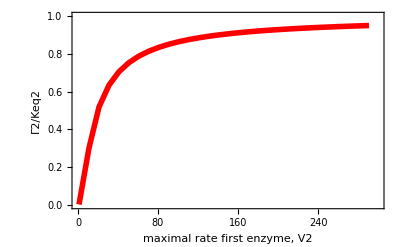

```mathematica
Table[{V2val,y[t]/(x[t] Keq2)/.parm1/.sschange1[V2,V2val]},{V2val,1,300,10}];
TableForm[%,TableHeadings->{None,{"V2","Γ2/Keq2"}}]
ListPlot[%,Joined->True,PlotRange->{{0,300},{0,1}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"maximal rate first enzyme, V2","Γ2/Keq2"},PlotStyle->{{Red,Thickness[0.01]}}]
```

So this shows that V2 equals 140.096 that this enzyme operates close to thermodynamic equilibrium,

```mathematica
y[t]/(x[t] Keq2)/.parm1/.sschange1[V2,140.096]
```

0.9

Increasing the Vmax further shifts the enzyme more equilibrium.

How far are the other enzymes from equilibrium?

```mathematica
x[t]/(s Keq1)/.parm1/.sschange1[V2,140.096]
p/(y[t] Keq3)/.parm1/.sschange1[V2,140.096]
```

0.000423938

0.000262093

So enzyme 1 is furthest from equilibrium, then enzyme 3 and then enzyme 2.

Model 2. 

In the previous model, the equilibrium constant of the first enzyme was set to 1.  We will now set it to 100 and determine again the value of the Vmax of the 2nd enzyme to have it 10% removed from thermodynamic equilibrium in steady state.

```mathematica
odes2={
x'[t]==v1-v2,
y'[t]==v2-v3};
rateqs2={
v1->((V1*s)/K1s(1-x[t]/(s Keq1)))/(1+s/K1s+x[t]/K1x),v2->((V2*x[t])/K2x(1-y[t]/(x[t] Keq2)))/(1+x[t]/K2x+y[t]/K2y),v3->((V3*y[t])/K3y(1-p/(y[t] Keq3)))/(1+y[t]/K3y+p/K3p)};
parm2={
(* enzyme 1 *)
V1->10,K1s->1,Keq1->1000,K1x->1,
(* enzyme 2 *)
V2->10,K2x->1,Keq2->100,K2y->1,
(* enzyme 3 *)
V3->10,K3y->1,Keq3->1000,K3p->1,
(* boundary conditions *)
s->10, p->1};
init2={
x[0]==1,y[0]==5};
vars2={x,y};
```

To determine the value of the equilibrium constant

```mathematica
parmchange2[param_,newvalue_]:=ReplacePart[parm2,Position[parm2,param][[1]][[1]]->param->newvalue]
```

```mathematica
tsolchange2[param_,newvalue_]:=NDSolve[Join[odes2/.rateqs2/.parmchange2[param,newvalue],init2],vars2,{t,0,100}]
```

```mathematica
sschange2[param_,newvalue_]:=FindRoot[Table[odes2[[i]][[2]]==0,{i,1, Length[odes2]}]/.rateqs2/.parmchange2[param,newvalue],Table[{vars2[[i]][t],(vars2[[i]][100]/.tsolchange2[param,newvalue])[[1]]},{i,1,Length[vars2]}]]
```

V2 | Γ2/Keq2
5000 | 0.839338
5500 | 0.851786
6000 | 0.862444
6500 | 0.871671
7000 | 0.879739
7500 | 0.886852
8000 | 0.89317
8500 | 0.898821
9000 | 0.903903
9500 | 0.9085
10000 | 0.912676

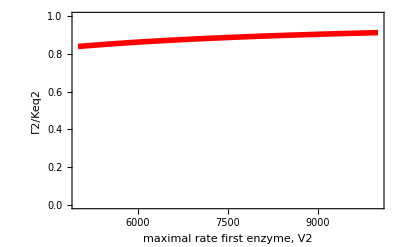

```mathematica
Table[{V2val,y[t]/(x[t] Keq2)/.parm2/.sschange2[V2,V2val]},{V2val,5000,10000,500}];
TableForm[%,TableHeadings->{None,{"V2","Γ2/Keq2"}}]
ListPlot[%%,Joined->True,PlotRange->{{5000,10000},{0,1}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"maximal rate first enzyme, V2","Γ2/Keq2"},PlotStyle->{{Red,Thickness[0.01]}}]
```

So this shows that V2 equals 8611.5 that this enzyme operates close to thermodynamic equilibrium,

```mathematica
y[t]/(x[t] Keq2)/.parm2/.sschange2[V2,8611.5]
```

0.9

Increasing the Vmax further shifts the enzyme more equilibrium.

How far are the other enzymes from equilibrium?

```mathematica
x[t]/(s Keq1)/.parm2/.sschange2[V2,8611.5]
p/(y[t] Keq3)/.parm2/.sschange2[V2,8611.5]
```

0.0000187246

0.0000593396

So enzyme 1 is furthest from equilibrium, then enzyme 3 and then enzyme 2.

In both models, the following relationship holds;
P/(S K_EQ1 K_EQ2 K_EQ3)=X/(S K_EQ1)Y/(X K_EQ2)P/(Y K_EQ3)
The models only differ in K_EQ2.  

The previous model comparison illustrated that an enzyme with a large equilibrium constant needs a higher Vmax (so more enzyme) to bring it close to equilibrium than an enzyme with a smaller Vmax.  This is a general rule.  Enzymes with small equilibrium constant often function close to thermodynamic equilibrium in metabolic pathways as the Vmax required for their operation close to equilibrium is small, with little enzyme this can achieved.

The models also differ in their steady state flux.

```mathematica
rateqs1/.parmchange1[V2,140.096]/.sschange1[V2,140.096]
rateqs2/.parmchange2[V2,8611.5]/.sschange2[V2,8611.5]
```

{v1→6.55916,v2→6.55916,v3→6.55916}

{v1→8.93858,v2→8.93858,v3→8.93858}

The second part of the question asks whether an enzyme close to equilibrium has a large effect on the steady state flux.  The best way to shows it plot the sensitivity coefficient of the flux to the maximal rate of enzyme 2 as function of its displacement from equilbrium.

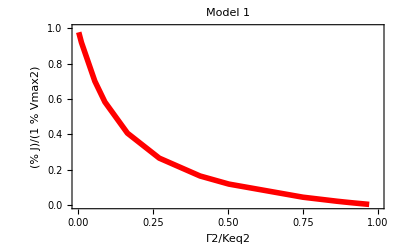

```mathematica
Table[{y[t]/(x[t] Keq2)/.parmchange1[V2,V2val]/.sschange1[V2,V2val],(((v1/.rateqs1/.parmchange1[V2,1.01*V2val]/.sschange1[V2,1.01*V2val])-(v1/.rateqs1/.parmchange1[V2,V2val]/.sschange1[V2,V2val]))/(v1/.rateqs1/.parmchange1[V2,V2val]/.sschange1[V2,V2val]))/0.01},{V2val,{1,2,4,5,7,10,15,20,50,100,125,150,175,200,500}}];
ListPlot[%,Joined->True,PlotRange->{{0,1},{0,1}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"Γ2/Keq2","(%  J)/(1  %  Vmax2)"},PlotStyle->{{Red,Thickness[0.01]}},PlotLabel->"Model 1"]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

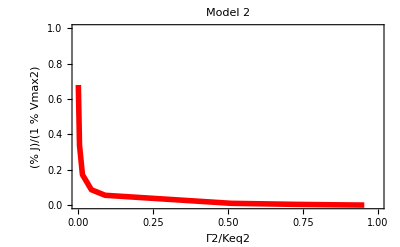

```mathematica
Table[{y[t]/(x[t] Keq2)/.parmchange2[V2,V2val]/.sschange2[V2,V2val],(((v1/.rateqs2/.parmchange2[V2,1.01*V2val]/.sschange2[V2,1.01*V2val])-(v1/.rateqs2/.parmchange2[V2,V2val]/.sschange2[V2,V2val]))/(v1/.rateqs2/.parmchange2[V2,V2val]/.sschange2[V2,V2val]))/0.01},{V2val,{5,10,20,50,100,1000,2500,5000,7500,8000,8250,8500,8550,8600,8650,8700,9000,10000,15000,20000}}];
ListPlot[%,Joined->True,PlotRange->{{0,1},{0,1}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"Γ2/Keq2","(%  J)/(1  %  Vmax2)"},PlotStyle->{{Red,Thickness[0.01]}},PlotLabel->"Model 2"]
```

So when an enzyme is close to thermodynamic equilibrium it has less effect on the steady state flux! Changes in the level of such an enzyme have little effect on the value of the steady state flux! Again this is a general rule.